# 弹簧与微分方程2

```mathematica
sol=NDSolveValue[{(x2[t]-x1[t])k-u m1 g x1'[t]==m1 x1''[t],(x1[t]-x2[t])k-u m2 g x2'[t]==m2 x2''[t],x1[0]=={-2,0},x2[0]=={2,0},x1'[0]=={0,2},x2'[0]=={0,-1}}/.{k->.5,g->9.8,u->0.05,m1->0.5,m2->0.80},{x1[t],x2[t]},{t,0,20}]
Manipulate[Show[ParametricPlot[sol,{t,0,20},PlotRange->2.2],Graphics[{Magenta,PointSize[Large],Point[sol/.t->tt]}]],{tt,0,20}]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

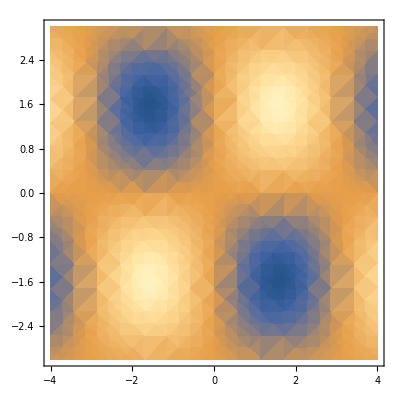

```mathematica
DensityPlot[Sin[x]Sin[y],{x,-4,4},{y,-3,3}]
```

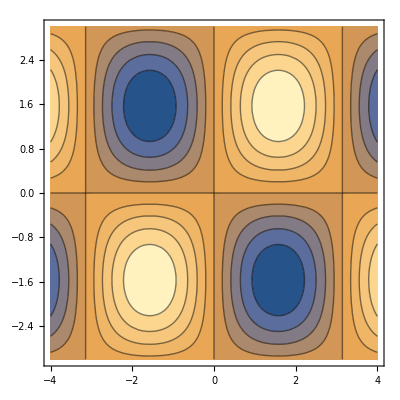

```mathematica
ContourPlot[Sin[x]Sin[y],{x,-4,4},{y,-3,3}]
```

```mathematica
Plot3D[Sin[x]Sin[y],{x,-4,4},{y,-3,3}]
```

-Graphics3D-